# MS-C1650 - Numerical Analysis Week 17: Lecture 3: A Gentle Introduction to Interpolation

## Harri Hakula, 2021

## Interpolation

Let us assume that we have a set of data points and we want to fit a polynomial which is exact at the data points. Consider a sine function.

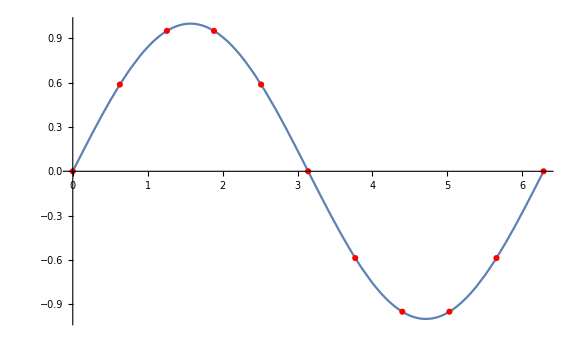

```mathematica
x=Subdivide[0,2Pi,10];
y=Sin[x];
Show[Plot[Sin[x],{x,0,2Pi}],ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic],ImageSize->Large]
```

```mathematica
poly=InterpolatingPolynomial[N@Transpose[{x,y}],t];
```

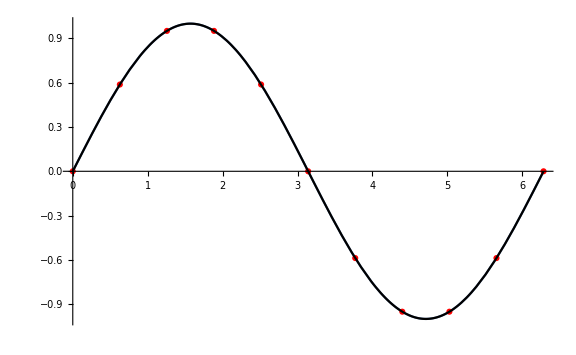

```mathematica
Show[Plot[Sin[x],{x,0,2Pi}],ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic],Plot[poly,{t,0,2Pi},PlotStyle->Black],ImageSize->Large]
```

```mathematica
err=Expand@N[poly-Normal@Series[Sin[t],{t,Pi,9}]]
```

-0.00692527+0.0232668 t-0.0343249 t^2+0.0290342 t^3-0.0154663 t^4+0.00537137 t^5-0.00121557 t^6+0.000172912 t^7-0.0000140419 t^8+4.96631×10^-7 t^9-2.31861×10^-18 t^10

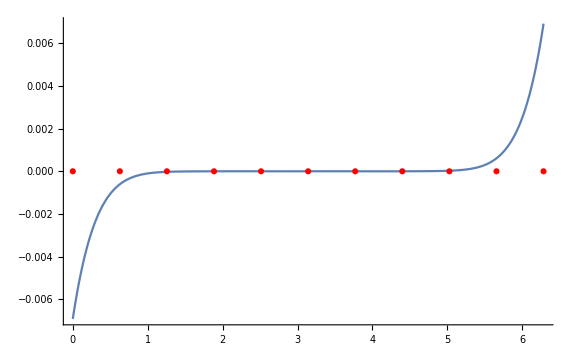

```mathematica
Show[Plot[err,{t,0,2Pi},PlotRange->All,ImageSize->Large],ListPlot[Thread[List[x,0]],PlotStyle->Red,PlotMarkers->Automatic]]
```

## Runge Phenomenon

The example above is misleading. Let us consider another example. (Notice that it is misleading in its own way!) The idea is to examine what happens when we increase the number of equidistant points.

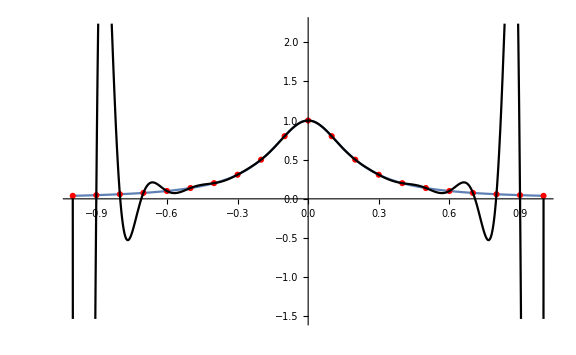

```mathematica
np=20;
x=Subdivide[-1,1,np];
y=1/(1+25x^2);
poly=InterpolatingPolynomial[N@Transpose[{x,y}],t];
Show[Plot[1/(1+25x^2),{x,-1,1}],ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic],Plot[poly,{t,-1,1},PlotStyle->Black],ImageSize->Large,PlotRange->All]
```

## Runge Phenomenon (Solution)

Now repeat the process above. By choosing the interpolation points appropriately, one can control the oscillations (and thus the error).

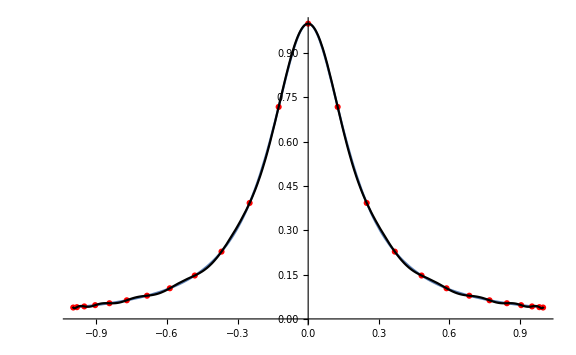

```mathematica
np=25;
xp=Table[Pi(2k-1)/(2np),{k,1,np}];
x=Cos[xp];
y=1/(1+25x^2);
poly=InterpolatingPolynomial[N@Transpose[{x,y}],t];
Show[Plot[1/(1+25x^2),{x,-1,1}],ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic],Plot[poly,{t,-1,1},PlotStyle->Black],ImageSize->Large]
```